# IIR Filter design

A popular method of creating digital filters is to transform analog prototypes to their digital equivalents using the bilinear transformation. The result is an infinite impulse response (IIR) filter, represented as a Trasfer Function Model (which is a discrete–time approximation of an analog filter)

## Analog Filters

### Butterworth

Two parameters:

cutoff frequency

filter order (sharpness of the transition)

Frequency response is monotonic,

```mathematica
ButterworthFilterModel[4]
tf=ToDiscreteTimeModel[ButterworthFilterModel[4],1,z]
poles=TransferFunctionPoles[tf]
```

```mathematica
1./(((0.3826834323650898-0.9238795325112867 ⅈ)+s) ((0.3826834323650898+0.9238795325112867 ⅈ)+s) ((0.9238795325112867-0.3826834323650898 ⅈ)+s) ((0.9238795325112867+0.3826834323650898 ⅈ)+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.0.38268343236508981FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
(1. (1.+z)^4)/((4.525594951964848+2.220446049250313*^-16 ⅈ)-(28.642488842966955-8.881784197001252*^-16 ⅈ) z+(74.68629150101523-1.7763568394002505*^-15 ⅈ) z^2-91.35751115703303 z^3+(56.78811354701991-2.8843107672476197*^-16 ⅈ) z^4)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111.4.5255949519648481FalseFalseFalseAutomaticNoneAutomatic
```

{{{0.345005+0.176037 ⅈ,0.345005-0.176037 ⅈ,0.459366-0.565866 ⅈ,0.459366+0.565866 ⅈ}}}

```mathematica
1./(((0.3826834323650898-0.9238795325112867 ⅈ)+s) ((0.3826834323650898+0.9238795325112867 ⅈ)+s) ((0.9238795325112867-0.3826834323650898 ⅈ)+s) ((0.9238795325112867+0.3826834323650898 ⅈ)+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.0.38268343236508981FalseFalseFalseAutomaticNoneAutomatic
```

{{{-0.92388-0.382683 ⅈ,-0.92388+0.382683 ⅈ,-0.382683-0.92388 ⅈ,-0.382683+0.92388 ⅈ}}}

```mathematica
1./(((0.5-0.8660254037844386 ⅈ)+s) ((0.5+0.8660254037844386 ⅈ)+s) (1.+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.0.51FalseFalseFalseAutomaticNoneAutomatic
```

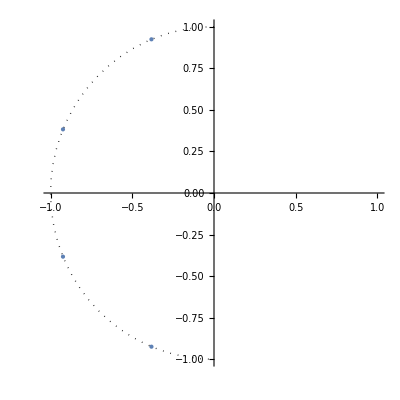

```mathematica
ListPlot[{Re[#],Im[#]}&/@poles[[1,1]],PlotRange->{{-1,1},{-1,1}},PlotStyle->PointSize[Large],Epilog->{Dotted,Circle[{0,0},1,{Pi/2,3Pi/2}]},AspectRatio->1,PlotRangePadding->0.1]
```

## Projektowanie filtrów cyfrowych Butterwortha i Czebyszewa

Układ analogowy jet stabilny, jeżeli bieguny jego transmitancji leżą w lewej półpłaszczyźnie płaszczyzny zespolonej

Układ dyskretny jest stabilny, jeżeli bieguny jego transmitancji leżą wewnątrz okręgu jednostkowego na płaszczyźnie zespolonej.

Dla układu analogowego osią częstotliwości jest oś urojona s=jω.
Dla układu dyskretnego częstotliwość zmiania się po okręgu jednostkowym z=e^jΩ.

W przypadku biegunów na osi (dla analogowych) lub na okręgu (dla dyskretnych) stabilność jest warunkowa, a układ odpowiada oscylacją.

Częstotliwość końca pasma przepustowego (f_P) w dB

Największe dopuszczalne tłumienie w paśmie przepustowym (A_p) dla filtru Czebyszewa ten parametr określa jednocześnie dopuszczalne zafalowanie charakterystyki amplitudowej w paśmie przepustowym (w kHz)

Częstotliwość początku pasma zaporowego (f_S) w dB

Wymagane minimalne tłumienie w paśmie zaporowym (A_s) (w kHz)

```mathematica
Ap=0.5; 
fp=3;
Ar=20;
fr=7;
```

### Obliczenie rzędu filtru

#### Współczynnik selektywności k

k=f_P/f_R

```mathematica
k[fp_,fr_]:=fp/fr;
```

#### Współczynnik dyskryminacji d

d=√((10^(0.1 A_P)-1)/(10^(0.1 A_R)-1))

```mathematica
d[Ap_,Ar_]:=√((10^(0.1 Ap)-1)/(10^(0.1 Ar)-1));
```

Rząd filtru Butterwortha oblicza się ze współczynników k i d

n=(|log d|)/(|log k|)

```mathematica
nbutt[d_,k_]:=Abs[Log[d]]/Abs[Log[k]];
```

```mathematica
nb=nbutt[d[Ap,Ar],k[fp,fr]]
```

3.95298

Rząd filtru Czebyszewa określa się z podobnego wzoru:

n=(arc cosh(1/d))/(arc cosh(1/k))

```mathematica
nczeb[d_,k_]:=ArcCos[1/d]/ArcCos[1/k];
```

```mathematica
nc=nczeb[d[Ap,Ar],k[fp,fr]]
```

2.71107+0. ⅈ

Rząd filtru nie może być ułamkowy, więc zaokrąglamy w górę.

```mathematica
nb=Ceiling[nb]
nc=Ceiling[nc]
```

4

3

Rząd filtr Czebyszewa będzie zawsze mniejszy lub równy rzędowi filtru Butterwortha

### Częstotliwość graniczna

W dolnoprzepustowym filtrze Czebyszewa jest to częstotliwość, dla której tłumienie filtru nie przekracza założonych zafalowań charakterystyki. A więc poprostu f_p

f_g=f_p

```mathematica
fgc=fp;
```

Dla filtru Butterwortha, częstotliwość graniczna to taka dla której następuje spadek wzmocnienia o 3 dB względem sygnału stałego (o częstotliowści 0). Jest ona większa od f_p jeżeli A_p jest mniejsze niż 3 dB. Można ją określić ze wzoru

f_g=f_p/((10^(0.1 A_p)-1)^(1/(2n)))

```mathematica
fg[fp_,Ap_,n_]:=fp/(10^(0.1 Ap)-1)^(1/(2n));
```

```mathematica
fgb=fg[fp,Ap,4]
```

3.90228

### Filtr prototypowy

Filtr prototypowy ≡ filtr anaologowy którego częstotliwość graniczna wynosi 1 Hz.

#### Butterworth

Kradraw charakterystyki amplitudowej definiuje się następująco

(|H(jω)|)^2=1/(1+(jω/j ω_(3 dB))^(2N))

|H(jω)|=√(1/(1+(jω/j ω_(3 dB))^(2N)))

gdzie ω_(3 dB) jest pulsacją, dla której charakterystyka amplitudowa opada do poziomu 1/(√2) (3 dB w skali decybelowej 20 log_10(1/√2)=-3dB. Rozważając zera mianownika:

1+(s/j ω_(3dB))^(2N)=0

Otrzymujemy bieguny transmitancji filtra Butterwortha:

```mathematica
sol=Solve[1+(s/(ⅈ ω))^(2NN)==0&&NN>0,s,Complexes]
```

{{s→ConditionalExpression[ⅈ ⅇ^((ⅈ (π+2 π C[1]))/(2 NN)) ω,(C[1]∈Integers&&-1+2 NN-2 C[1]≥0&&C[1]≥0)||(C[1]∈Integers&&C[1]≤-1&&1+2 NN+2 C[1]>0)]}}

```mathematica
sol[[1,1,2,1]]
```

ⅈ ⅇ^((ⅈ (π+2 π C[1]))/(2 NN)) ω

ω_(3dB)ⅇ^(j (π/(2N))(2k+N-1))

Do filtru wybieramy tylko te znajdujące się w lewej półpłaszczyźnie

```mathematica
roots[k_,N_]:=Exp[ⅈ(π/(2N))(2k+N-1)];
NN=2;
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
1/Times[selrootbutt/.{List->Sequence}]
```

1/(((0.707107-0.707107 ⅈ)+s) ((0.707107+0.707107 ⅈ)+s))

Z równania (Section.EquationNumbered) otrzymujemy:

20 log_10(1/√(1+(ω_p/ω_(3dB))^(2N)))=-A_p

20 log_10(1/√(1+(ω_s/ω_(3dB))^(2N)))=-A_s

Skąd rząd filtru:

N=1/2 log_10((10^(A_p/10)-1)/(10^(A_s/10)-1))/log_10(ω_p/ω_s)

ω_(3dB)=ω_pass/((10^(A_p/10)-1)^(1/(2N)))

### Składanie w całość dla Butterworth

```mathematica
Ap=0.5; 
fp=3;
As=20;
fs=7;
```

```mathematica
NButterworth[Ap_,As_,fp_,fs_]:=Ceiling[1/2 Log10[(10^(Ap/10)-1)/(10^(As/10)-1)]/Log10[fp/fs]];
```

```mathematica
f3dB[fp_,Ap_,NN_]:=fp/((10^(Ap/10)-1)^(1/(2NN)));(**pulsacja**)
```

```mathematica
NN=NButterworth[Ap,As,fp,fs]
f3dB[fp,Ap,NN]
```

4

3.90228

```mathematica
roots[k_,N_]:=f3dB[fp,Ap,NN]Exp[ⅈ(π/(2N))(2k+N-1)];
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
ButterworthFilter[ω_]:=f3dB[fp,Ap,NN]^NN/Times[selrootbutt/.{List->Sequence}]/.{s->ⅈω}
```

231.885/(((1.49334-3.60523 ⅈ)+ⅈ ω) ((1.49334+3.60523 ⅈ)+ⅈ ω) ((3.60523-1.49334 ⅈ)+ⅈ ω) ((3.60523+1.49334 ⅈ)+ⅈ ω))

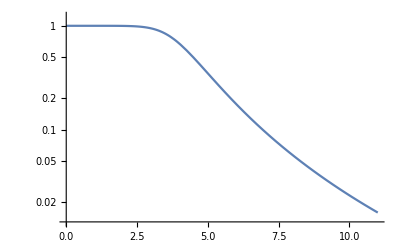

```mathematica
ButterworthFilter[ω]
LogPlot[Abs[ButterworthFilter[ω]],{ω,0,11},PlotRange->Full]
```

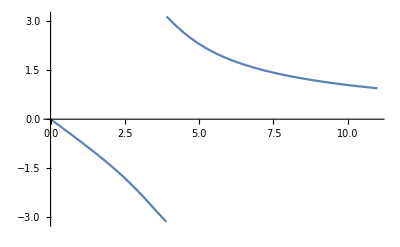

```mathematica
Plot[Arg[ButterworthFilter[ω]],{ω,0,11},PlotRange->Full]
```

### Dla Czebyszewa

(|H(jω)|)^2=1/(1+ϵ^2 V_N^2(ⅈω/ⅈ ω_(3dB)))

Gdzie

V_N(x)=Piecewise[{{cos(N arccos(x)), |x|≤1}, {cosh(Narccosh(x)), |x|>1}}]

Jest to filtr I typu. Charakterystyka jest równomiernie falista w paśmie przepustowym.
Amplituda zafalowania jest regulowana parametrem ϵ. 
W paśmie zaporowym charakterystyka opada monotonicznie

Dla filtru typu II jest odwrotnie. Charakterystyka jest płaska w paśmie przepustowym i równomiernie falista w paśmie zaporowym. 
Parametr ϵ reguluje amplitudę zafalowania charakterystyki amplitudowej w paśmie zaporowym.

(|H(jω)|)^2=1/(1+1/(ϵ^2 V_N^2(ⅈω_(3dB)/ⅈω)))

### Filtr eliptyczny

Do aproksymacji idealnej, prostokątnej charakterystyki częstotliwościowej w przypadku filtra eliptycznego stosuje się eliptyczną funkcję Jacobiego. 
Charakterystyka amplitudowa filtra eliptycznego jest równomiernie falista w paśmie przepustowym i zaporowym. Filtr eliptyczny opisują 4 parametry: N – rząd filtra, ω - krawędź pasma przepustowego, A_p oraz A_s.

### Transformacja częstotliwości

Low pass | s'=s/ω_0
High pass | s'=ω_0/s
Band pass | s'=ω_0/Δω((s/ω_0)^2+1)/(s/ω_0)
Band stop | s'=Δω/ω_0(s/ω_0)/((s/ω_0)^2+1)

where Δω=ω_2-ω_1 and ω_0=√(ω_1 ω_2)

### Transformacja biliniowa

s=2/Δt((1-z^-1)/(1+z^-1))

```mathematica
z/.Solve[s==2/Δt((1-z^-1)/(1+z^-1)),z][[1]]
```

(-2-s Δt)/(-2+s Δt)

ω=2/Δt tg(Ω/2)

Ω=arc tg(ω Δt/2)

## Projekt filtru dolnoprzepustowego

częstotliwość próbkowania f_pr=100Hz
krawędź pasma przepustowego f_1=20Hz
krawędź pasma zaporowego f_2=25Hz
nieliniowość charakterystyki w paśmie przepustowym r_p=3 dB
nieliniowość charakterystyki w paśmie zaporowym r_s=30dB

Przeliczenie częstotliwości filtra cyfrowego f_1 i f_2 na pulsację Ω w radianach:

Ω_1=2π f_1/f_pr=2π 20/100=1.2566 rad

Ω_2=2π f_2/f_pr=2π 25/100=1.5708 rad

```mathematica
A1=3;
f1=20;
A2=30;
f2=25;
fp=100;
```

```mathematica
Ω1=N@2π f1/fp
Ω2=N@2π f2/fp
```

1.25664

1.5708

### Krawędź pasma filtru analogowego

ω_1=2/(2Δt)tan(Ω_1/2)=2/(1/100)tan(1.2566/2)=145.3085 rad/s

ω_2=200 rad/s

```mathematica
ω1=2/(1/fp)Tan[Ω1/2]
ω2=2/(1/fp)Tan[Ω2/2]
fa1=1/(2π)ω1;
fa2=1/(2π)ω2;
```

145.309

200.

### Określenie parametrów filtru analogowego na podstawie podanych wymagań

```mathematica
NButterworth[Ap_,As_,fp_,fs_]:=Ceiling[1/2 Log10[(10^(Ap/10)-1)/(10^(As/10)-1)]/Log10[fp/fs]];
```

```mathematica
f3dB[fp_,Ap_,NN_]:=fp/((10^(Ap/10)-1)^(1/(2NN)));(**pulsacja**)
```

```mathematica
NN=NButterworth[A1,A2,fa1,fa2]
N@f3dB[ω1,A1,NN]
```

11

145.34

```mathematica
roots[k_,N_]:=f3dB[ω1,A1,NN]Exp[ⅈ(π/(2N))(2k+N-1)];
rootsbutt=N@Table[roots[i,NN],{i,0,NN}];
selrootbutt=s-Select[rootsbutt,Re[#]<=0&];
ButterworthFilter[ω_]:=f3dB[ω1,A1,NN]^NN/Times[selrootbutt/.{List->Sequence}]
```

### Filtr analogowy

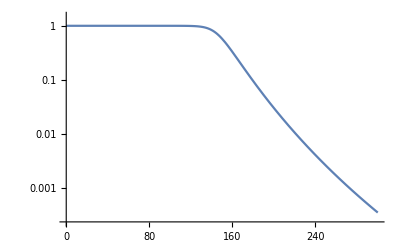

```mathematica
LogPlot[{Abs[ButterworthFilter[s]/.{s->ⅈ ω}]},{ω,0,300},PlotRange->Full]
```

### Przejście na filtr cyfrowy (w dziedzienie pulsacji/częstości)

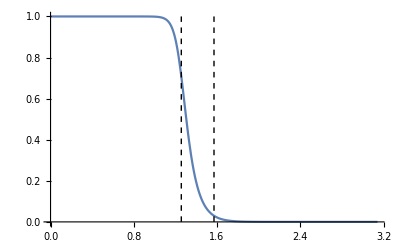

```mathematica
Plot[Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}],{Ω,0,π},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{Ω1,0},{Ω1,1}}],Line[{{Ω2,0},{Ω2,1}}]}]
```

```mathematica
N@1/10^(3/10)
N@1/10^(30/10)
```

0.501187

0.001

### Filtr cyfrowy w dziedzinie częstotliwości

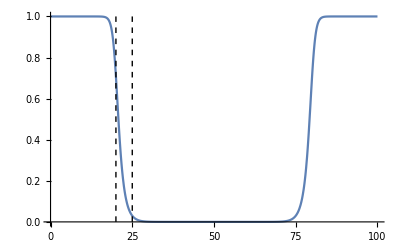

```mathematica
Plot[Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}/.{Ω->f (2π)/fp}],{f,0,100},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{f1,0},{f1,1}}],Line[{{f2,0},{f2,1}}]}]
```

## Reakcja filtru Butterworth na częstotliwości odcięcia

```mathematica
Manipulate[NButterworth[A1,A2,x,y],{x,0,100},{y,x,100},{A1,0,100,1},{A2,0,100,1}]
```

Obserwacja: im częstotliwości bliższe sobie, a za tem im bardziej stromy filtr tym wyższy rząd filtru Butterworth’a jest wymagany.

Oprócz tego dla:
(2.2,2.3)→N=78
(22.2,22.3)→N=769
(82.2, 82.3)→N=2843
a więc rząd filtru rośnie także z częstotliwością przy stałej różnicy f_2-f_1.

## Analiza filtrów Butterwortha w Mathematica

```mathematica
DiscretizeData[x_,bits_]:=Module[{max},max=Max[Abs[x]]; If[#>0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x];
```

```mathematica
num=Numerator@ButterworthFilter[s];
```

```mathematica
Denominator@ButterworthFilter[s]
```

((20.684-143.861 ⅈ)+s) ((20.684+143.861 ⅈ)+s) ((60.3764-132.206 ⅈ)+s) ((60.3764+132.206 ⅈ)+s) ((95.1774-109.841 ⅈ)+s) ((95.1774+109.841 ⅈ)+s) ((122.268-78.5767 ⅈ)+s) ((122.268+78.5767 ⅈ)+s) ((139.453-40.947 ⅈ)+s) ((139.453+40.947 ⅈ)+s) (145.34+s)

```mathematica
reals=Re[#]&/@(s/.Solve[Denominator@ButterworthFilter[s]==0,s])
imags=Im[#]&/@(s/.Solve[Denominator@ButterworthFilter[s]==0,s])
```

{-145.34,-139.453,-139.453,-122.268,-122.268,-95.1774,-95.1774,-60.3764,-60.3764,-20.684,-20.684}

{0,-40.947,40.947,-78.5767,78.5767,-109.841,109.841,-132.206,132.206,-143.861,143.861}

```mathematica
coeffs=Join[reals,imags];
{realsD,imagsD}=Partition[DiscretizeData[coeffs,6],Length@coeffs/2]
```

{{-143.861,-139.22,-139.22,-120.657,-120.657,-97.4539,-97.4539,-60.3286,-60.3286,-18.5626,-18.5626},{0.,-41.766,41.766,-78.8913,78.8913,-111.376,111.376,-129.939,129.939,-143.861,143.861}}

```mathematica
denomD=s-(realsD+ⅈ imagsD)/.{List->Times}
```

((18.5626-143.861 ⅈ)+s) ((18.5626+143.861 ⅈ)+s) ((60.3286-129.939 ⅈ)+s) ((60.3286+129.939 ⅈ)+s) ((97.4539-111.376 ⅈ)+s) ((97.4539+111.376 ⅈ)+s) ((120.657-78.8913 ⅈ)+s) ((120.657+78.8913 ⅈ)+s) ((139.22-41.766 ⅈ)+s) ((139.22+41.766 ⅈ)+s) ((143.861+0. ⅈ)+s)

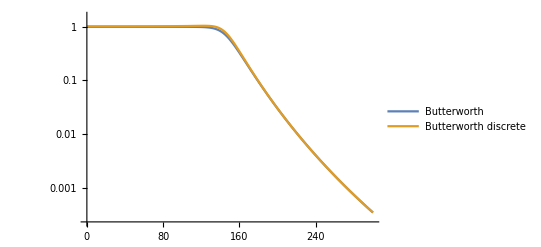

```mathematica
LogPlot[{Abs[ButterworthFilter[s]/.{s->ⅈ ω}],Abs[num/denomD/.{s->ⅈω}]},{ω,0,300},PlotRange->Full,PlotLegends->{"Butterworth","Butterworth discrete"}]
```

W dziedzinie pulsacji, łatwiej będzie obliczyć błąd

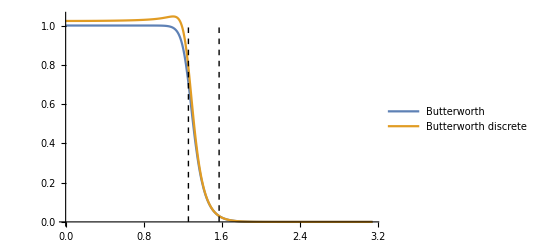

```mathematica
Plot[{Abs[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}],Abs[num/denomD/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]},{Ω,0,π},PlotRange->Full,Epilog->{Dashing[0.01],Line[{{Ω1,0},{Ω1,1}}],Line[{{Ω2,0},{Ω2,1}}]},PlotLegends->{"Butterworth","Butterworth discrete"}]
```

```mathematica
CalcError[filtr_,filtrD_]:=Sqrt[NIntegrate[Abs[filtr-filtrD]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]/NIntegrate[Abs[filtr]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]]
```

```mathematica
CalcError[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ},num/denomD/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]
```

0.0439729

Uzyskaliśmy w ten sposób średni błąd względny dla pewnego filtru Butterwortha, przy dyskretyzacji do 8-miu bitów.
Teraz uogólnimy tę procedurę i wykreślimy błąd w zależności od ilości bitów

### Błąd w zależności od ilości bitów

```mathematica
filtersD=Table[num/(MapThread[s-(#1+ⅈ #2)&,Partition[DiscretizeData[coeffs,i],Length@coeffs/2]]/.{List->Times}),{i,4,32,2}];
```

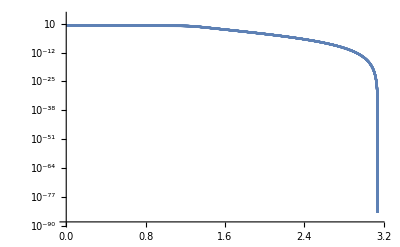

```mathematica
LogPlot[Abs[#/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]&/@filtersD,{Ω,0,π},PlotRange->Full]
```

```mathematica
errors=CalcError[ButterworthFilter[s]/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ},#/.{s->2fp(1-z^-1)/(1+z^-1)}/.{z->ⅇ^ⅈΩ}]&/@filtersD
```

{0.0807374,0.0439729,0.00941541,0.0052734,0.000730413,0.000199079,0.0000632721,3.97357×10^-6,6.46014×10^-7,5.85675×10^-7,1.50606×10^-7,5.29091×10^-8,5.92378×10^-9,1.83285×10^-9,9.99849×10^-11}

```mathematica
bits=Range[4,32,2];
```

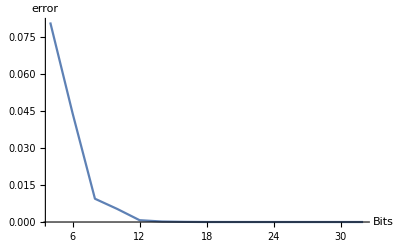

```mathematica
ListLinePlot[{bits,errors}ᵀ,PlotRange->Full,AxesLabel->{"Bits","error"}]
```

## Analiza względem wszystkich parametrów

Badanie rzędu filtru Butterwortha, Czebyszewa i Eliptycznego

```mathematica
q[k_]:=u+2 u^5+15 u^9+150 u^13/.{u->(1-(1-k^2)^(1/4))/(2(1+(1-k^2)^(1/4)))}
```

```mathematica
Manipulate[Plot3D[{1/2 Log10[(10^(A1/10)-1)/(10^(A2/10)-1)]/Log10[x],ArcCosh[1/(√((10^(A1/10)-1)/(10^(A2/10)-1)))]/ArcCosh[1/x],Log10[16(10^(A1/10)-1)/(10^(A2/10)-1)]/Log10[1/q[x]]},{x,0.000001,1},{A1,1,A2},AxesLabel->{"f_1/f_2","A1","N"},PlotLegends->{"Butterworth","Czebyszev","Eliptic"},ImageSize->Large,PlotRange->{{0,1},{1,A2},{0,15}}],{A2,2,100}]
```

Jak widać filtr eliptyczny może mieć nawet rząd zero, gdyż oprócz biegunów ma także zera

-((0.320579+5.91413×10^-18 ⅈ) ((0.-1.43991 ⅈ)+s) ((0.+1.43991 ⅈ)+s))/(((0.161497-1.00334 ⅈ)+s) ((0.161497+1.00334 ⅈ)+s) ((0.643573+0. ⅈ)+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-0.320578806561637950.161497094869716641FalseFalseFalseAutomaticNoneAutomatic

1.96523/(((0.353724-1.08865 ⅈ)+s) ((0.353724+1.08865 ⅈ)+s) ((0.926062-0.672824 ⅈ)+s) ((0.926062+0.672824 ⅈ)+s) (1.14468+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s111.96522672836027160.35372430057723431FalseFalseFalseAutomaticNoneAutomatic

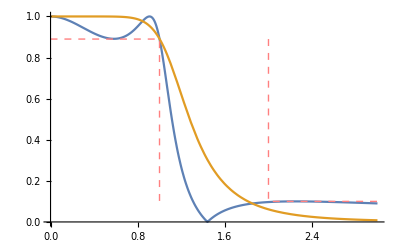

```mathematica
tf=EllipticFilterModel[{"Lowpass",{1.,2.},{1.,20}}]
tf2=ButterworthFilterModel[{"Lowpass",{1.,2.},{1.,20}}]
Plot[{Abs[tf[I*ω]],Abs[tf2[I*ω]]},{ω,0,3},PlotRange->All,Epilog->{Pink,Dashed,Line[{{0,0.89},{1,0.89},{1,0.1}}],Line[{{2.,0.89},{2.,0.1},{3.,0.1}}]}]
```

```mathematica
DiscretizeList[x_,bits_]:=Module[{max},max=Max[Abs[x]]; If[#>=0,1,-1]Round[(Abs[#]/max)(Power[2,bits-1]-1)] max/(Power[2,bits-1]-1) &/@x];
DiscretizeComplexList[x_,bits_]:=Module[{reals,imags,coeffs,realsD,imagsD},
If[x=={},{},
reals=Re[#]&/@x;
imags=Im[#]&/@x;
coeffs=Join[reals,imags];
{realsD,imagsD}=Partition[DiscretizeList[coeffs,bits],Length@coeffs/2];
(realsD+ⅈ imagsD)]
];
CalcError[filtr_,filtrD_]:=Sqrt[NIntegrate[Abs[filtr-filtrD]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]/NIntegrate[Abs[filtr]^2,{Ω,0,π},AccuracyGoal->5,MaxRecursion->20]];
```

```mathematica
DiscretizedModel[tf_,bits_]:=Module[{tfD,coeff,zeros,poles},
coeff=First@Flatten[Chop@Coefficient[Numerator[tf[s]],s,0]];
zeros=(s/.Solve[Numerator@(tf[s])==0,s])/.{s->{}};
poles=(s/.Solve[Denominator@(tf[s]/coeff)==0,s]);
coeff(s-DiscretizeComplexList[zeros,bits]/.{List->Times})/(s-DiscretizeComplexList[poles,bits]/.{List->Times})
];
```

```mathematica
models=Table[ButterworthFilterModel[{"Lowpass",{1.,1./k},{i,20}},s],{k,0.1,0.9,0.01},{i,1,12,0.5}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
```

```mathematica
ListPlot3D[errors,DataRange->{{0.1,0.9},{1,12}},AxesLabel->{"k","A1","Error"},ImageSize->Large]
```

-Graphics3D-

```mathematica
models=Table[Chebyshev1FilterModel[{"Lowpass",{1.,1./k},{i,20}},s],{k,0.1,0.9,0.01},{i,1,12,0.5}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
ListPlot3D[errors,DataRange->{{0.1,0.9},{1,12}},AxesLabel->{"k","A1","Error"},ImageSize->Large]
```

-Graphics3D-

```mathematica
models=Table[EllipticFilterModel[{"Lowpass",{1.,1./k},{i,20}},s],{k,0.1,0.9,0.01},{i,1,12,0.5}];
modelsD=Map[(DiscretizedModel[#,6])&,models,{2}];
errors=MapThread[First@Flatten@CalcError[#1[I Ω],#2/.{s->I Ω}]&,{models,modelsD},2];
ListPlot3D[errors,DataRange->{{0.1,0.9},{1,12}},AxesLabel->{"k","A1","Error"},ImageSize->Large]
```

-Graphics3D-